```mathematica
DSolve[(1-x^2)y''[x]-2x y'[x]+a(a+1)y[x]==0,y[x],x]
```

{{y[x]→C[1] LegendreP[a,x]+C[2] LegendreQ[a,x]}}

```mathematica
y1=LegendreP[a,x];
y2=LegendreQ[a,x];
```

```mathematica
Series[y1,{x,0,5}]
```

(√π)/(Gamma[1/2-a/2] Gamma[1+a/2])+(a (1+a) √π x)/(2 Gamma[1-a/2] Gamma[3/2+a/2])+((-1+a) a (1+a) (2+a) √π x^2)/(8 Gamma[3/2-a/2] Gamma[2+a/2])+((-2+a) (-1+a) a (1+a) (2+a) (3+a) √π x^3)/(48 Gamma[2-a/2] Gamma[5/2+a/2])+((-3+a) (-2+a) (-1+a) a (1+a) (2+a) (3+a) (4+a) √π x^4)/(384 Gamma[5/2-a/2] Gamma[3+a/2])+((-4+a) (-3+a) (-2+a) (-1+a) a (1+a) (2+a) (3+a) (4+a) (5+a) √π x^5)/(3840 Gamma[3-a/2] Gamma[7/2+a/2])+O[x]^6

```mathematica
Series[y2,{x,0,5}]
```

-(√π Gamma[(1+a)/2] Sin[(a π)/2])/(2 Gamma[(2+a)/2])+(√π Cos[(a π)/2] Gamma[1+a/2] x)/Gamma[(1+a)/2]+((a+a^2) √π Gamma[(1+a)/2] Sin[(a π)/2] x^2)/(4 Gamma[(2+a)/2])-(((-2+a+a^2) √π Cos[(a π)/2] Gamma[1+a/2]) x^3)/(6 Gamma[(1+a)/2])-(((-6 a-5 a^2+2 a^3+a^4) √π Gamma[(1+a)/2] Sin[(a π)/2]) x^4)/(48 Gamma[(2+a)/2])+((24-14 a-13 a^2+2 a^3+a^4) √π Cos[(a π)/2] Gamma[1+a/2] x^5)/(120 Gamma[(1+a)/2])+O[x]^6

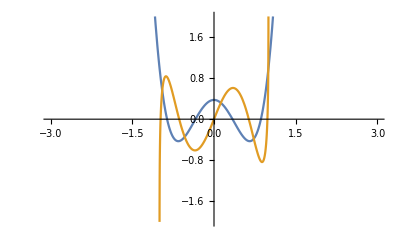

```mathematica
a0=4;
Plot[{y1/.{a->a0},y2/.{a->a0}},{x,-3,3},PlotRange->{-2,2}]
```

```mathematica
W=Wronskian[{y1,y2},x]
```

-((1+a) (LegendreP[1+a,x] LegendreQ[a,x]-LegendreP[a,x] LegendreQ[1+a,x]))/(-1+x^2)

```mathematica
W/.{a->20}//FullSimplify
```

1/(1-x^2)

```mathematica
?Series
```

Series[f,{x,x_0,n}] generates a power series expansion for f about the point x=x_0 to order (x-x_0)^n. 
Series[f,{x,x_0,n_x},{y,y_0,n_y},…] successively finds series expansions with respect to x, then y, etc.